```mathematica
ClearAll["Global`*"]

runIndex =3;


runNames = { "disc_shear", "hawk_moth", "buckeye_butterfly"}; 
 runName = runNames[[runIndex]]
MeshDir = FileNameJoin[{NotebookDirectory[] ,"Mesh Data"(*,"2D"*), runName}];
resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];


numTimeSteps = 30; timeSteps = Range[numTimeSteps] - 1;

spatialDim = 2;

getFaceNaibs[faces_] := (

neibs[face_]:= (l = Position[(Length[Intersection[face, #]] ==2)& /@ faces, True]//Flatten;
If[Length[l]==2, AppendTo[l, 0]];
Return [l]
);

neibs/@faces
)


(* an (internal) edge will connect two faces*)
getEdgeList[faces_] :=(

edges = {};

checkNeibs[face_]:=(Length[Intersection[face, #]] ==2)& /@ faces;

es= checkNeibs /@ faces;

 DeleteDuplicates[Sort/@ Position[es, True]]
)





makeDelta1[numFaces_][edge_]:=(row = ConstantArray[0,numFaces];
row[[edge[[1]]]] = 1.0; row[[edge[[2]]]] = -1.0;
row
)
makeDeltaFaces[numFaces_, edges_]:= (

makeDelta1[numFaces]/@edges
)



makeAvg1[areas_, numFaces_][edge_]:=(row = ConstantArray[0,numFaces];
(*areas = getAreas[vertices, faces];*)
α = areas[[edge[[1]]]]/(areas[[edge[[1]]]] +  areas[[edge[[2]]]]);

row[[edge[[1]]]] = α; row[[edge[[2]]]] = 1 -α;
row
)
makeAvgFaces[areas_,numFaces_, edges_]:= (

makeAvg1[areas,numFaces]/@edges
)



getArea[faceVerts_]:=(
v1 = Append[ faceVerts[[2]]- faceVerts[[1]],0];
v2 = Append[ faceVerts[[3]]- faceVerts[[1]],0];

0.5 Norm[Cross[v1,v2]]
)
getAreas[vertices_, faces_]:=(
getArea /@ (vertices[[#]]&/@faces)
)


makeEdgeMatrix[vertices_, edges_, faces_] := (

areas = getAreas[vertices, faces];

makeRow[edge_]:= ({face1, face2} = faces[[edge]];
{ind0, ind1} = Intersection[face1, face2];
ind2 = Complement[face1, face2][[1]];
ind3 = Complement[face2, face1][[1]];

P0 = vertices[[ind0]]; P1= vertices[[ind1]];
P2 = vertices[[ind2]]; P3= vertices[[ind3]];

V0 = P1 - P0; V1 = P2 - P0; V2 = P3 - P0;

U = ConstantArray[0, {Length[faces], spatialDim}];

U[[edge[[1]]]] = V0/6 - V1/3; U[[edge[[2]]]] = -V0/6 + V2/3; 

Flatten[U/Sqrt[areas]]

);

SparseArray[makeRow /@ edges]
)



computeGradSqrMatrix[vertices_, edges_, faces_]:= (
(*get the centroid positions*)
centroids = Mean[vertices[[#]]] &/@faces;

(*deltaFaces is a matrix (numEdges x numFaces) giving the difference in values between faces connected by an edge*)
deltaFaces = makeDeltaFaces[Length[faces],edges];
(*avgFaces is a matrix (numEdges x numFaces) giving the average between values between faces connected by an edge*)
(*avgFaces = makeAvgFaces[Length[faces],edges];*)


M = makeEdgeMatrix[vertices, edges, faces];


MSol = PseudoInverse[M].deltaFaces;

Transpose[MSol].MSol

(*Graphics[{Opacity[0.5],EdgeForm[Thickness[0.001]],Opacity[0.1],Yellow,Triangle[vertices[[#]]&/@faces],Opacity[0.7], Red, Line[centroids[[#]]&/@edges],Blue, Point[centroids]}]*)
)


(*Make a Gaussian filter from a set of centroid points in a mesh
width is given relative to the maximum dimension of the mesh*)
getGaussianFilter[ vertices_,edges_,faces_, width_:0.05]:=
(

 centroids = Mean[vertices[[#]]] &/@faces;


g = Graph[edges, EdgeWeight->((EuclideanDistance[centroids[[#[[1]]]],centroids[[#[[2]]]]])&/@edges)];

distMat = GraphDistanceMatrix[g];


maxDist = Max[distMat];
filterWidth = width*maxDist;


F[d_]:= Chop[Exp[-d^2/(2 filterWidth^2)]];
weights =F[distMat];
gaussianFilter = #/Total[#]&/@weights

)


saveGaussianFilters[timeIndex_]:=(

SetDirectory[FileNameJoin[{MeshDir ,("time" <> ToString[timeIndex])}]];

faces = Import["faces.csv" ]  + 1;

edges = Import["faceEdges.csv"] + 1;

verts= Import["vertices.csv"];


gFilter = getGaussianFilter[verts,edges, faces];
Export["GaussianFilter.csv", gFilter];

)


getMaxDims[]:=(



getMax[timeIndex_]:=(
SetDirectory[FileNameJoin[{MeshDir ,("time" <> ToString[timeIndex])}]];

verts=Import["vertices.csv"];

xDim = Max [verts[[;;,1]]] - Min[verts[[;;,1]]];
yDim = Max [verts[[;;,2]]] - Min[verts[[;;,2]]];

{xDim, yDim}

);

maxDims = Max /@ Transpose[getMax/@ timeSteps];

SetDirectory[resultDir];
Export["MaxDimensions.csv", maxDims];

)


getLandMarks[]:=(
SetDirectory[MeshDir];

landMarks = Import["landmark.txt", "Data"] - 1;
Export["landmarks.csv", landMarks];
)


getBoundaryLengths[vertices_, faces_, boundaryIndx_]:=(

getLength[bInd_]:=(
neibVerts0 = DeleteDuplicates[Select[faces, MemberQ[#, bInd]&]//Flatten];

neibVerts = DeleteCases[Select[neibVerts0,MemberQ[boundaryIndx, #]& ], bInd];

length = 0.5(EuclideanDistance[  vertices[[bInd]],vertices[[  neibVerts[[1]]  ]]  ]    + EuclideanDistance[  vertices[[bInd]],vertices[[  neibVerts[[2]]  ]]  ]  )

);

getLength /@ boundaryIndx
)


getNormFactor[]:= (
SetDirectory[FileNameJoin[{MeshDir ,"time0"}]];
verts0= Import["vertices.txt", "Data"];
faces0= Import["faces_new.txt", "Data"] - 1;

areas0 = getAreas[verts0, faces0  +1];
 1/Sqrt[Total[areas0]]
)


importExport[timeIndex_]:=(

norm = getNormFactor[];

SetDirectory[FileNameJoin[{MeshDir ,("time" <> ToString[timeIndex])}]];

inds = (Import["boundary_indices.txt", "Data"]//Flatten) - 1;
Export["boundary_indices.csv", inds];


faces= Import["faces_new.txt", "Data"] - 1;
Export["faces.csv", faces];

verts1= Import["vertices.txt", "Data"];
centerVert = Mean[verts1];
verts = norm*(Transpose[Transpose[verts1] - centerVert]);
Export["vertices.csv", verts];


vertsD0 = Import["vertices_deformed.txt", "Data"];
vertsD= norm*(Transpose[Transpose[vertsD0] - centerVert]);
Export["vertices_deformed.csv", vertsD];


areas = getAreas[verts, faces + 1];
Export["faceAreas.csv", areas];



boundaryDisps = vertsD[[inds + 1]]  - verts[[inds + 1]];
Export["boundary_displacements.csv", boundaryDisps];

normal= Import["normal.txt", "Data"];
Export["normal.csv", normal];


fEdges = getEdgeList[faces ] - 1;
Export["faceEdges.csv", fEdges];

gradCostMat = computeGradSqrMatrix[verts, fEdges + 1, faces + 1];
Export["gradCostMat.csv", gradCostMat];

bndryLengths = getBoundaryLengths[verts, faces + 1, inds + 1];
Export["boundaryLengths.csv", bndryLengths];


(*faceNeibs = getFaceNaibs[faces] - 1;
Export["facesNeibs.csv", faceNeibs];


*)


)

(*getLandMarks[]*)

importExport/@timeSteps
getMaxDims[]

saveGaussianFilters/@timeSteps

(*
*)
```

buckeye_butterfly

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
(*getVertexAreas[vertices_, faces_, areas_]:= (
vertIndices = Range[Length[vertices]];
faceIndices = Range[Length[faces]];

getVArea[vIndx_]:=( fInd = DeleteDuplicates[Select[faceIndices, MemberQ[faces[[#]], vIndx]&]];

vArea = Total[areas[[fInd]]]/3
);

(getVArea /@ vertIndices)//Flatten
)
*)


loadData[timeIndex_]:=(

SetDirectory[FileNameJoin[{MeshDir ,("time" <> ToString[timeIndex])}]];

faces = Import["faces.csv" ]  + 1;

verts= Import["vertices.csv"];

areas = Import["faceAreas.csv"]//Flatten

(*bInds = 1 + Import["boundary_indices.csv"]//Flatten;

getBoundaryLengths[verts, faces, bInds]*)


(*getVertexAreas[verts, faces, areas]
*))




 vAs = loadData[20];

Total[vAs]

(*m = computeGradSqrMatrix[v,e,f];*)
```

1.

```mathematica
Total[areas]
```

{3.13788}

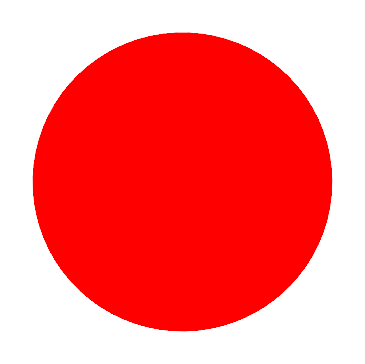

```mathematica
Graphics[{PointSize[0.001],Red, Point[verts], EdgeForm[Thick], Triangle[verts[[#]]&/@faces]}]
```